# Brownian Tree

#### Task

A Brownian tree is generated as a result of an initial seed, followed by the interaction of two processes

The initial “seed” is placed somewhere within the field. Where is not particularly important. It could be randomized or it could be a fixed point.

Particles are injected into the field, and are individually given a (typically random) motion pattern.

When a particle collides with the seed or tree, its position is fixed, and it’s considered to be part of the tree

Might try to use CreateDataStructure[“DynamicArray”]

#### Strategy

Create a matrix of 0s

Create n particles at random positions on the matrix

Create n random movements

Use MapIndexed to check if particle+movement already takes up a spot

If it does, then make particle take a spot, remove it from set of particles.

If it doesn’t then nothing happens.

Continue step 4 until out of particles

Use MatrixPlot to create the tree.

```mathematica
treeTouch[{i_,j_},{index_}]:=With[
{atpos=positions[[i,j]]},
If[atpos>0,
Apply[positions[[#1,#2]]++&,particles[[index]]];
positions[[i,j]]++;
index,
{}]]


zoomIn[m_?SquareMatrixQ]:=Module[{d=Dimensions[m],c,t},
c=Ceiling[Dimensions[m]/2];
t={
MinMax@Table[If[m[[i,All]]!=ConstantArray[0,d[[1]]],i,c],{i,d[[1]]}],
MinMax@Table[If[m[[All,i]]!=ConstantArray[0,d[[2]]],i,c],{i,d[[2]]}]
};
m[[t[[1,1]];;t[[1,2]],t[[2,1]];;t[[2,2]]]]
]
```

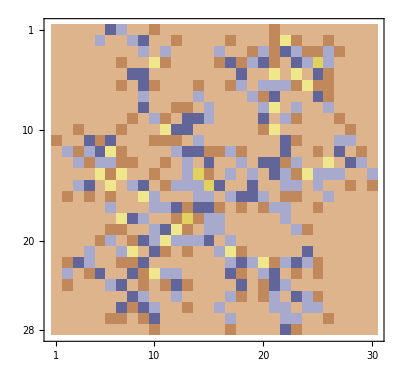

```mathematica
d=30;
n=Floor[0.35*d^2];
seed={Ceiling[d/2],Ceiling[d/2]};
positions=ConstantArray[0,{d,d}];
Apply[positions[[#1,#2]]++&,seed];(*RandomInteger[{1,d},2]*)
particles=RandomInteger[{1,d},{n,2}];
particles=DeleteCases[particles,seed];


Monitor[
While[Length[particles]>0,
(*Moves each particle randomly and then test if it would go outside of the box. If it does, then it is set to the limits.*)
movement=particles+RandomInteger[{-1,1},{Length[particles],2}]/.{x_?NonPositive->1,x_/;Greater[x,d]->d};
(*Deletes the particle if it becomes attached to the tree*)
particles=Delete[movement,
ArrayReshape[#,{Length[#],1}]&@
Flatten@MapIndexed[treeTouch[#1,#2]&,movement]];
particlepos=SparseArray[Thread[particles->-1],{d,d}];
plot=MatrixPlot[positions+particlepos,ColorFunction->"DarkBands"]
],plot]
positions//zoomIn//MatrixPlot[#,ColorFunction->"DarkBands"]&
```